```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/sse_cos_test.dat"]//Flatten;
len=dat0//Length;
korak=2*Pi/(len-1);
xval=Table[-Pi+korak*i,{i,0,len-1}];
exactCos=Table[{xval[[i]],Cos[xval[[i]]]},{i,0,xval//Length}];
diff=Table[{xval[[i]],Cos[xval[[i]]] - dat0[[i]]},{i,0,xval//Length}];
```

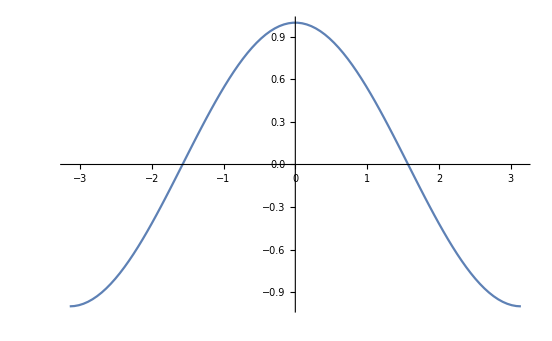

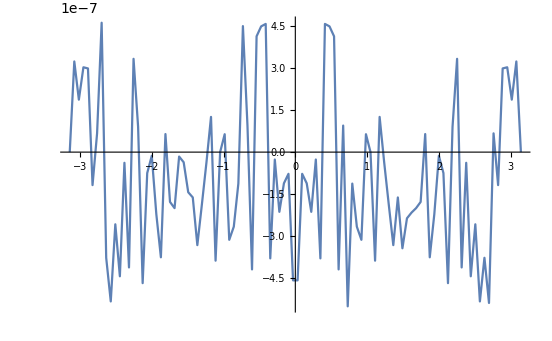

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}]}]
ListLinePlot[diff]
```

```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/sse_sin_test.dat"]//Flatten;
len=dat0//Length;
korak=2*Pi/(len-1);
xval=Table[-Pi+korak*i,{i,0,len-1}];
exactCos=Table[{xval[[i]],Sin[xval[[i]]]},{i,0,xval//Length}];
diff=Table[{xval[[i]],Sin[xval[[i]]] - dat0[[i]]},{i,0,xval//Length}];
```

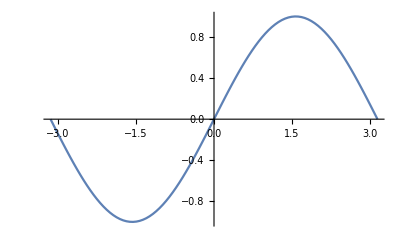

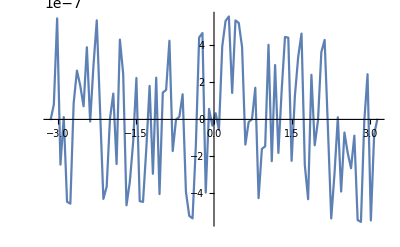

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}]}]
ListLinePlot[diff]
```

```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/avx_cos_test.dat"]//Flatten;
len=dat0//Length;
korak=2*Pi/(len-1);
xval=Table[-Pi+korak*i,{i,0,len-1}];
exactCos=Table[{xval[[i]],Cos[xval[[i]]]},{i,0,xval//Length}];
diff=Table[{xval[[i]],Cos[xval[[i]]] - dat0[[i]]},{i,0,xval//Length}];
```

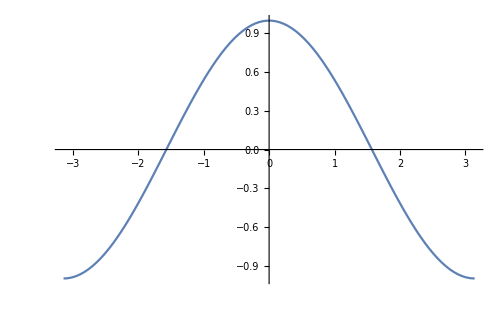

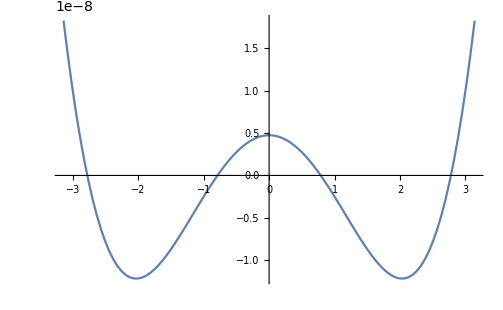

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}]}]
ListLinePlot[diff]
```

```mathematica
coeff=Table[2/Pi*NIntegrate[Cos[Pi*Cos[theta]]*Cos[m*theta],{theta, 0,Pi}, WorkingPrecision->40,AccuracyGoal->40, MaxRecursion->1000],{m,0,26,2}];
coeff[[1]]=coeff[[1]]/2;
coeff
```

{-0.3042421776440938642020349128177049239697,-0.9708678652630182194109914323663784757039,0.3028491552626994215074191186309676140775,-0.02909193396501112114732073920800360778849,0.001392243991176231859984622208952274539411,-0.00004018994451075494298816526236368837878949,7.782767011815306088573057896947073998291×10^-7,-1.08265303418582848109342149267869577559×10^-8,1.135109177911507701030194019523024834037×10^-10,-9.295296632678756552885410084526215786661×10^-13,6.111364188334767723806229076684641965132×10^-15,-3.297657841343458986382435554107381460019×10^-17,1.486813423673207704795437109347570207022×10^-19,-5.685578136847164353761054026365713383437×10^-22}

```mathematica
coeff=Table[2/Pi*NIntegrate[Sin[Pi*Cos[theta]]*Cos[m*theta],{theta, 0,Pi}, WorkingPrecision->40,AccuracyGoal->40, MaxRecursion->1000],{m,1,31,2}];
coeff
```

{0.5692306863595055146906211993722628114196,-0.6669166724059790707804371634797734966045,0.1042823687342369494809202521862043939116,-0.006840633536991579009851374503285063910684,0.0002500068849503862276522158590075481730046,-5.850248308639143691717116193971950655104×10^-6,9.534772750299401140044067750300658462647×10^-8,-1.145638441709463151347564618146685930344×10^-9,1.057427261753912858869898216472797435085×10^-11,-7.735270995404307094156646286268862437722×10^-14,4.595956146182959459195691643430204238586×10^-16,-2.262305928197411104312660436182426308008×10^-18,9.377647799153135796251624441737014705742×10^-21,-3.318599491698564909515356552225801325484×10^-23,1.014380222196161580311718419311112037293×10^-25,-2.705193531668109420814186495894754642391×10^-28}

```mathematica
SetPrecision[ChebyshevT[5,{1.0,2.5,3.6,4.8}], 20]
```

{1.,1262.5,8759.4681600000003527,38580.794879999994009}

```mathematica
im[a_]:=34459425*a-4729725*a^3+135135*a^5-990a^7 +a^9
st[a_]:=34459425-16216200*a^2 +945945a^4-13860*a^6+45*a^8
```

```mathematica
T9[a_]:=im[a]/st[a]
```

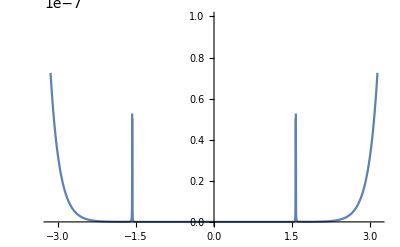

```mathematica
Plot[Abs[T9[a]-Tan[a]],{a, -Pi, Pi}, PlotRange->{0, 10^-7}]
```

```mathematica
SetPrecision[Tan[{-0.7, -0.3, 0.33, 1.553}], 20]
SetPrecision[im[{-0.7, -0.3, 0.33, 1.553}], 20]
```

{-0.84228838046307941134,-0.30933624960962324835,0.3425248675300389678,56.185438688872594071}

{-2.252193247404660657×10^7,-1.0210453086556682363×10^7,1.1202166556932132691×10^7,3.699934455378305167×10^7}

```mathematica
S[n_, t_]:=Block[{},
expression=Collect[Integrate[LegendreP[11,t]*Sin[t],t], Cos[t]];
k=expression/.Cos[t]->0/.Sin[t]->1;
l=expression/.Cos[t]->1/.Sin[t]->0;
Return[l/k]
]
```

```mathematica
S[5,t]
```

(3604742431983 t-600790405215 t^3+30039519510 t^5-715224510 t^7+9930635 t^9-88179 t^11)/(33 (-109234619151+54617309565 t^2-4551442350 t^4+151714290 t^6-2708355 t^8+29393 t^10))